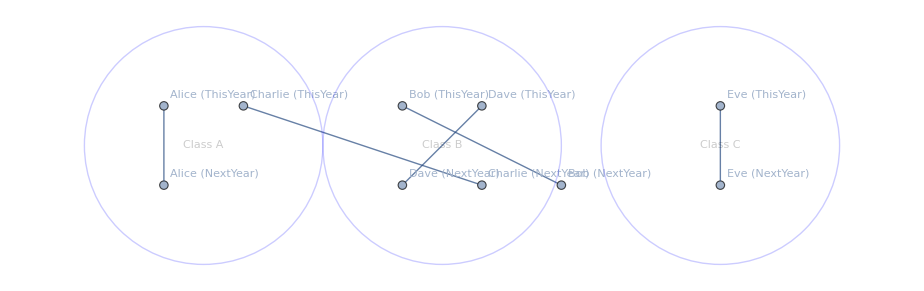

```mathematica
(*Sample Data*)thisYearData={{"Alice","Class A"},{"Bob","Class B"},{"Charlie","Class A"},{"Dave","Class B"},{"Eve","Class C"}};
nextYearData={{"Alice","Class A"},{"Bob","Class C"},{"Charlie","Class B"},{"Dave","Class B"},{"Eve","Class C"}};

(*Function to create unique player identifiers with class*)
makeUnique[player_,year_]:=StringJoin[player," (",year,")"]

(*Create edges between the same players across years*)
edges=Flatten[Table[If[thisYear[[1]]===nextYear[[1]],{UndirectedEdge[makeUnique[thisYear[[1]],"ThisYear"],makeUnique[nextYear[[1]],"NextYear"]]},{}],{thisYear,thisYearData},{nextYear,nextYearData}]];

(*Nodes for each year*)
thisYearNodes=Table[makeUnique[player[[1]],"ThisYear"],{player,thisYearData}];
nextYearNodes=Table[makeUnique[player[[1]],"NextYear"],{player,nextYearData}];
allNodes=Join[thisYearNodes,nextYearNodes];

(*Manual Node Positioning by Class*)
positions=Association[makeUnique["Alice","ThisYear"]->{0,1},makeUnique["Charlie","ThisYear"]->{1,1},makeUnique["Alice","NextYear"]->{0,0},makeUnique["Charlie","NextYear"]->{1,0},makeUnique["Bob","ThisYear"]->{3,1},makeUnique["Dave","ThisYear"]->{4,1},makeUnique["Bob","NextYear"]->{5,0},makeUnique["Charlie","NextYear"]->{4,0},makeUnique["Dave","NextYear"]->{3,0},makeUnique["Eve","ThisYear"]->{7,1},makeUnique["Eve","NextYear"]->{7,0}];

(*Create the graph*)
graph=Graph[allNodes,edges,VertexLabels->"Name",VertexCoordinates->positions];

(*Calculate cluster circles*)
clusters={{"Class A",{0.5,0.5}},{"Class B",{3.5,0.5}},{"Class C",{7,0.5}}};
circleGraphics=Graphics[{Opacity[0.2],Blue,Circle[#,1.5]&/@clusters[[All,2]],Black,Text[#[[1]],#[[2]]]&/@clusters}];

(*Combine the graph and the cluster circles*)
Show[graph,circleGraphics]
```

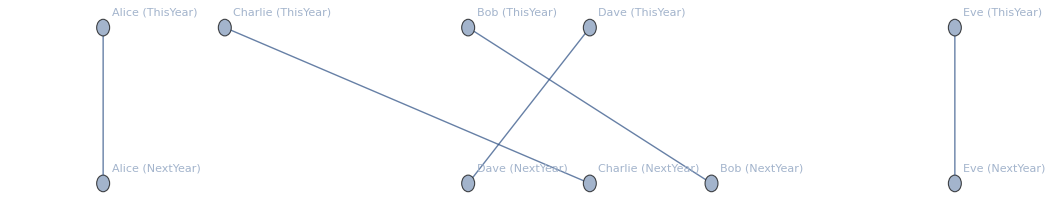

```mathematica
graph
```

```mathematica
(*Sample Data:Nodes and Edges*)nodes={"Alice","Bob","Charlie","Dave","Eve","Frank"};
edges={UndirectedEdge["Alice","Bob"],UndirectedEdge["Alice","Charlie"],UndirectedEdge["Bob","Charlie"],UndirectedEdge["Charlie","Dave"],UndirectedEdge["Dave","Eve"],UndirectedEdge["Eve","Frank"],UndirectedEdge["Frank","Alice"]};

(*Define Communities*)
communities={{"Alice","Bob","Charlie"},{"Dave","Eve","Frank"}};

(*Specify Vertex Coordinates*)
vertexCoordinates={"Alice"->{0,0},"Bob"->{1,0},"Charlie"->{0.5,1},"Dave"->{2,0},"Eve"->{3,0},"Frank"->{2.5,1}};

(*Community Graph Plot*)
communityGraphPlot=CommunityGraphPlot[Graph[nodes,edges],communities,GraphLayout->"MultipartiteEmbedding",VertexCoordinates->vertexCoordinates,VertexLabels->"Name",PlotTheme->"Detailed",CommunityRegionStyle->{LightBlue,LightGreen}];

(*Display the Graph*)
communityGraphPlot
```

-Graphics-

```mathematica
thisYearNodes=Table[makeUnique[player[[1]],"ThisYear"],{player,thisYearData}]
```

{Alice (ThisYear),Bob (ThisYear),Charlie (ThisYear),Dave (ThisYear),Eve (ThisYear)}